```mathematica
filesAR=FileNames["/home/carla/GDC/AUS/GDC_Conf_AR_AUS_DOJ_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/AUS/GDC_Conf_BR_AUS_DOJ_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{0.0434783,3,69},{0.142857,3,21},{1.,1,1}}

{{0.0116279,3,258},{0.142857,3,21}}

```mathematica
dojAR=confAR[[All,1]]
dojBR=confBR[[All,1]]
```

{0.0434783,0.142857,1.}

{0.0116279,0.142857}

```mathematica
sList={6,7,8};
sList2={6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
```

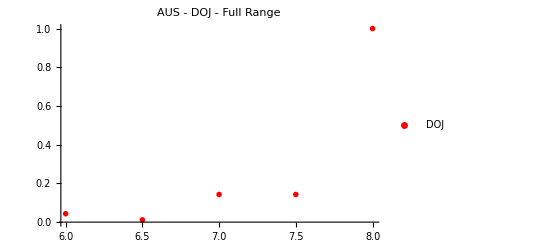

```mathematica
PlotDOJAllParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"AUS - DOJ - Full Range", PlotMarkers->{{"D",12}}]
```

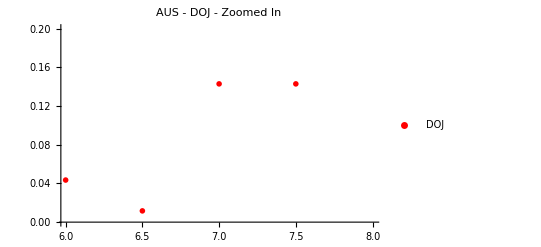

```mathematica
PlotDOJParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->{0.0, 0.2},  PlotLabel->"AUS - DOJ - Zoomed In",  PlotMarkers->{{"D",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/AUS/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"AUS_DOJ.txt"]
Export["AUS_DOJ.jpeg",PlotDOJAllParts,ImageSize->850]
Export["AUS_DOJ_Zoomed_In.jpeg",PlotDOJParts,ImageSize->850]
```

AUS_DOJ.jpeg

AUS_DOJ_Zoomed_In.jpeg